# Latent Space

Understanding latent variables and how they applied in machine learning.

Pavlo Apisov, Jun. 27,  2018

In the world of machine learning, dimensionality is a serious thing to consider because in some cases the more dimensions in data the harder it could be to learn and generalize.

Latent space helps us by compressing data and/or representing it in more meaningful ways.

Latent variables are broadly used in generative models or whenever you need to learn high-level representation of data.

## Meaningful data

Adding a conceptual meaning to data is the most important quality of latent space representation.

Your input data(observable variables) is in the space that you can observe and you want to find connection of this data to a latent space(hidden variables) where similar data points closer to each other.

Let’s draw 4 differently colored figures and treat them as our input  data:

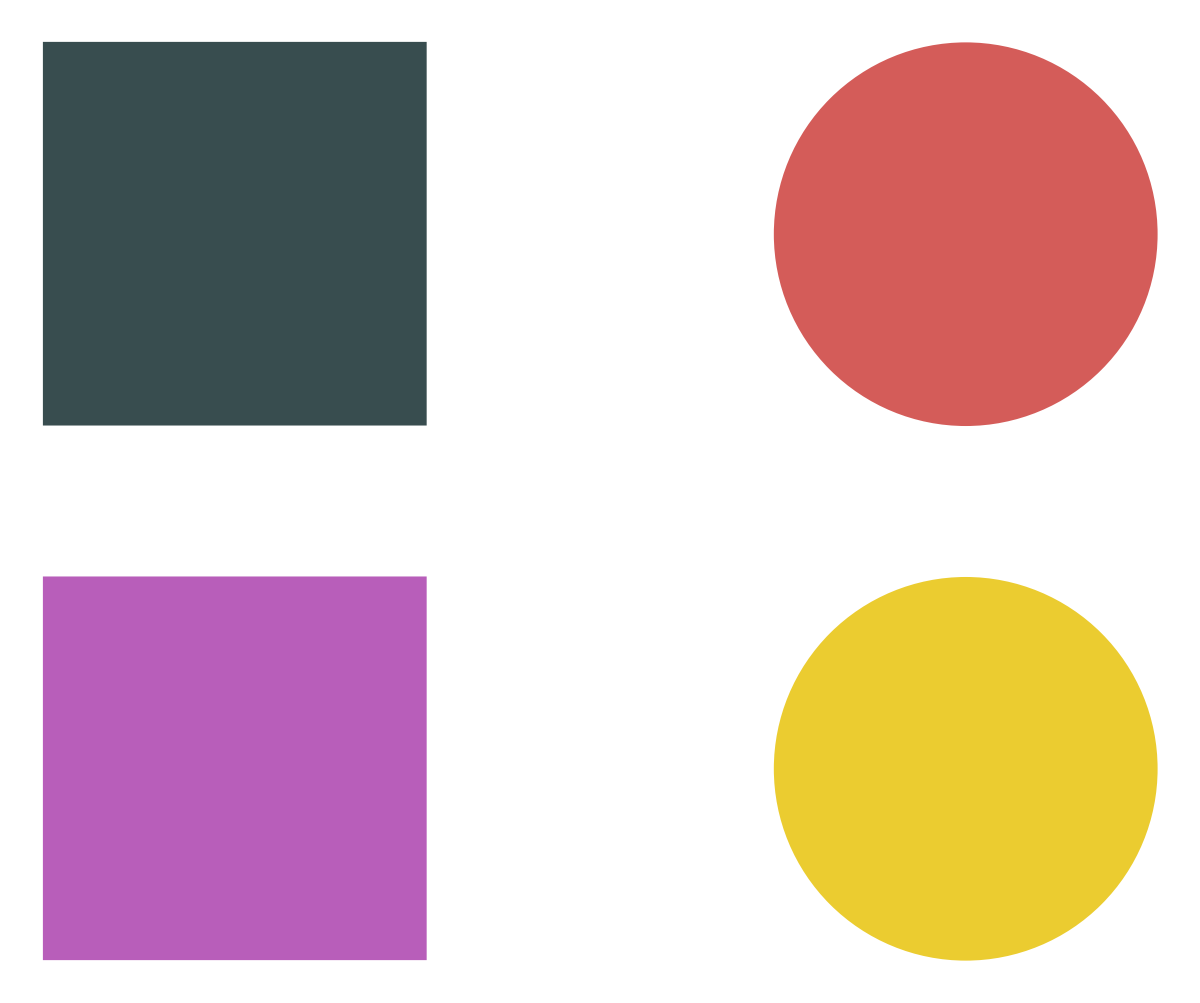

```mathematica
GraphicsGrid[{{Graphics[{RGBColor[0.22, 0.3, 0.31],Rectangle[]}], Graphics[{RGBColor[0.83, 0.36, 0.35],Disk[]}]}, {Graphics[{RGBColor[0.72, 0.37, 0.73],Rectangle[]}],Graphics[{RGBColor[0.92, 0.8, 0.19],Disk[]}]}}, Spacings->{200,50}]
```

As an example, in the pixel space that you observe, there is no similarity between any two figures above.

If we plot the observable space of the data we see a random layout.

```mathematica
FeatureSpacePlot[{Graphics[{RGBColor[0.22, 0.3, 0.31],Rectangle[]}], Graphics[{RGBColor[0.83, 0.36, 0.35],Disk[]}], Graphics[{RGBColor[0.72, 0.37, 0.73],Rectangle[]}],Graphics[{RGBColor[0.92, 0.8, 0.19],Disk[]}]}, ImageSize->{120,120}]
```

-Graphics-

Nevertheless, if we try to connect the data to a latent space you would want rectangles to be closer to each other in the latent space than to any of circles.

To do so, we should build our latent space observing shape of figures.

In our case we use edge detection to construct a latent space representation

```mathematica
FeatureSpacePlot[{Graphics[{RGBColor[0.22, 0.3, 0.31],Rectangle[]}], Graphics[{RGBColor[0.83, 0.36, 0.35],Disk[]}], Graphics[{RGBColor[0.72, 0.37, 0.73],Rectangle[]}],Graphics[{RGBColor[0.92, 0.8, 0.19],Disk[]}]}, ImageSize->{120,120}, FeatureExtractor->EdgeDetect]
```

-Graphics-

To recapitulate, latent space captures the structure of your data with respect to your task.

I.e for image classification problem, you want to connect images to a latent vector space such that images with similar meaning(pictures of cat, for example) are closer in that space.

## Section Header

Or show an example of application ...

Another way to start an exposition, or to expand on the basics, is to provide an example showing the application of the topic. The example might be something you arrive at by the end of the exposition, repeating that conclusion here is acceptable if it's reasonably self-contained. It might also be an example a problem scenario and the exposition explains a solution.

Always have code text as a lead-in to code that follows, to concisely indicate what it does:

```mathematica
Code (* demonstrate a specific application *)
```

## Section Header

Add more sections as needed to explain the topic....

Section names, the total number of sections, and section organization will differ based on the topic.

Here are some ideas for sections you might consider:

history/origins

derivation

applications

common misunderstandings

recent developments

unanswered questions

## Further explorations

Name of a related topic for exploration

Name of another related topic for exploration (repeat as needed)

## Author contact information

Email: apisovp@gmail.com

Twitter: apisov_pavlo

GitHub: apisov

## Guidelines for the Author

### Image

Try to use images created in the Wolfram Language as much as possible

If an external image is the only way to go, use Import to get the image into the notebook and reverse close the In/Out cell-group  to hide the input cell.

### Text

Use minimal text in small pieces to explain the topic and transition between pieces of code. One or two lines of text at a time should suffice.

Sub-guideline two

### CodeText

Before each line of code, add a single line in CodeText style, as a lead-in, to say what the code that follows will do.

End this line with a colon

Make a map of Monaco:

```mathematica
GeoGraphics[Entity["Country","Monaco"]]
```

-Graphics-

### Code

Keep code simple and straightforward; code cell should be at most 3 lines long

Breakup complicated lengthy code into multiple segments and separate with CodeText lead-ins explaining each segment

Try to create simple visualizations whenever possible to illustrate the topic and add visual interest

Extra code (for example, visualization options to simply make the output look pretty) can be distracting and take away focus from the main functionality. Either avoid these or use Iconize to hide them.

Instead of

```mathematica
Plot[Sin[x], {x, 1, 10}, PlotStyle -> {Red, Dashed, Thick}]
```

Use

```mathematica
Plot[Sin[x],{x,1,10},]
```

If using a Manipulate, remember to set SaveDefinitions->True, if it refers to definitions not contained within it. This will allow the Manipulate to work without having to re-evaluate the notebook, for every new session.

Include Data Repository

Include Function Repository (mention coming soon)